Abs[x]^(1/3)

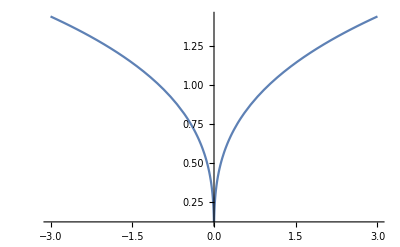

```mathematica
f[x_]=Abs[x^(1/3)]
Plot[f[x],{x,-3,3}]
```

```mathematica
derivada[x_]=1/3*Abs[x^(-2/3)]
Plot[derivada[x],{x,-1,1}]
```

1/(3 Abs[x]^(2/3))

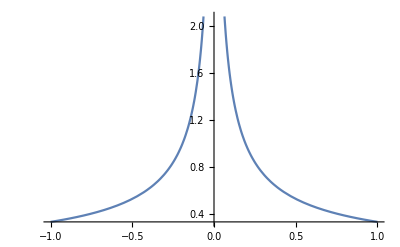

Piecewise[{{1, 0<x<1}, {-x, -1<x<0}, {0, True}}]

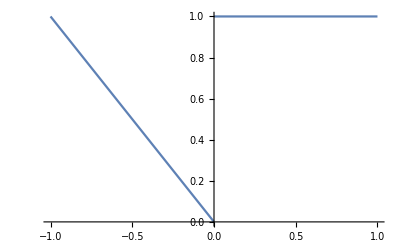

```mathematica
(*Conclusión:no es suave a tramos, es continua a tramos, pero no suave a tramos ya que no existen los limites laterales en cero*)
g[x_]=Piecewise[{{1,0<x<1},{-x,-1<x<0}}]
Plot[g[x],{x,-1,1}]
```

Piecewise[{{0, 0<x<1}, {-1, -1<x<0}, {0, True}}]

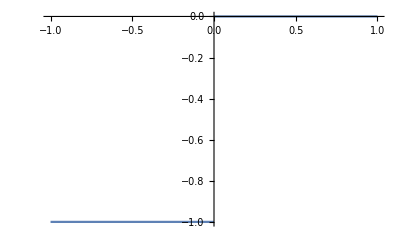

```mathematica
dg[x_]=Piecewise[{{0,0<x<1},{-1,-1<x<0}}]
Plot[dg[x],{x,-1,1}]
```

```mathematica
(*Conclusión: si es continua a tramos y tambien suave a tramos*)
```

Piecewise[{{Tan[1/x], 0<x<1}, {-1, -1<x<0}, {0, True}}]

Piecewise[{{-1/((1+1/x^2) x^2), 0<x<1}, {0, True}}]

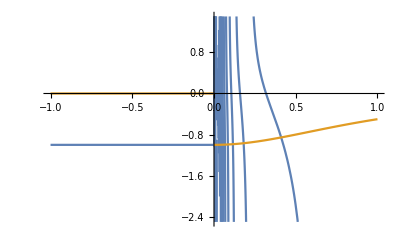

```mathematica
h[x_]=Piecewise[{{Tan[1/x],0<x<1},{-1,-1<x<0}}]
dh[x_]=Piecewise[{{-1/(x^2*(1+1/x^2)),0<x<1},{0,-1<x<0}}]
Plot[{h[x],dh[x]},{x,-1,1}]
```

```mathematica
(*Conclusión:No es suave a tramos ya que no existe el limite cuando la funcion tiende a cero*)
```